```mathematica
(* MATH 68500
Michael Barile
10/2/17 *)
(* Problem #1 *)
f[x_]:=x*Exp[-x]-1;
fprime[x_]=D[f[x],x];
fprime2[x_]=D[f[x],x,x];
fprime3[x_]=D[f[x],x,x,x];
t[x_]:=f[2.5]+fprime[2.5]*(x-2.5)+1/2*fprime2[2.5]*(x-2.5)^2+1/6*fprime3[2.5]*(x-2.5)^3;
normIntErrT=Sqrt[Integrate[(f[x]-t[x])^2,{x,1,4}]];
meanNormIntErrT=1/3*normIntErrT;
Print["The norm interpolation error is ",normIntErrT];
Print["The mean norm interpolation error is ",meanNormIntErrT];
```

The norm interpolation error is 0.0187681

The mean norm interpolation error is 0.00625605

```mathematica
(* Problem #2 *)
(* a. *)
A={};
For[i=1,i≤4,++i,
inew={};
For[j=0,j≤3,++j,
AppendTo[inew,i^j]
];
A=Append[A,inew]
];
b=Table[f[i],{i,1,4}];
coef=LinearSolve[A,b];
p[x_]:=coef[[1]]+coef[[2]]*x+coef[[3]]*x^2+coef[[4]]*x^3;
Print["The polynomial interpolation is ",N[p[x],6]];
```

The polynomial interpolation is -0.628323+0.0660124 x-0.0813614 x^2+0.0115519 x^3

The polynomial interpolation is -0.628323+0.0660124 x-0.0813614 x^2+0.0115519 x^3

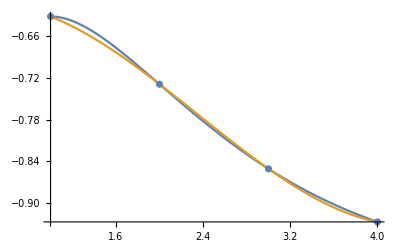

```mathematica
(*b*)
Show[Plot[{f[x],p[x]},{x,1,4}],ListPlot[{{1,p[1]},{2,p[2]},{3,p[3]},{4,p[4]}}]]
```

```mathematica
(* c*)
normIntErrP=N[Sqrt[Integrate[(f[x]-p[x])^2,{x,1,4}]],6];
meanNormIntErrP=1/3*normIntErrP;
Print["The norm interpolation error is ",normIntErrP];
Print["The mean norm interpolation error is ",meanNormIntErrP];
```

The norm interpolation error is 0.00748051

The mean norm interpolation error is 0.0024935

```mathematica
(*d*)
If[normIntErrP<normIntErrT,Print["The polynomial interpolation is a better fit for f than the cubic Taylor."],Print["The cubic Taylor is a better fit for f than the polynomial interpolation."]
];
```

The polynomial interpolation is a better fit for f than the cubic Taylor.

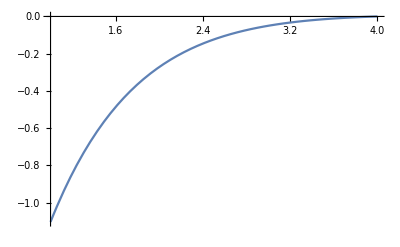

```mathematica
(* e *)
fprime4[x_]=D[f[x],x,x,x,x];
Plot[fprime4[x],{x,1,4}]
```

```mathematica
M=Abs[fprime4[1]];
n=3;a=1;b=4;
maxError=M/((n+1)!)*(b-a)^(n+1);
Print["The maximal absolute error is less than or equal to ", N[maxError,6]];
```

The maximal absolute error is less than or equal to 3.72478